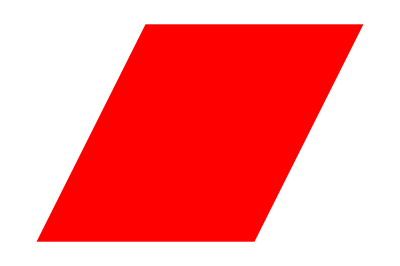

```mathematica
Graphics[{Red, Parallelogram[{0, 0}, {{1/2, 1}, {1, 0}}]}]
```

```mathematica
a = {1, 0, 0};
b = 1/2{1, √3, 0};
origin = {0, 0, 0};

crossDiagram =Graphics3D[{
Opacity[.5], (* Makes area of Parallelogram transparent *)
Yellow,
Polygon[{origin, a, a+b,  b}], (* Forms Parallelogram made by a and b*)
Opacity[1], 
Blue, 
Arrow[{origin, a}], (* Vector a *)
Red, 
Arrow[{origin, b}], (* Vector b *)
Purple, 
Arrow[{origin, Cross[a, b]}] (* Vector a × b *)
}]; 
Show[crossDiagram, Boxed -> False]
```

-Graphics3D-

-Graphics3D-

```mathematica
Show[cross_diagram,FaceGrids->All]
```

Show::gtype: Pattern is not a type of graphics.

Show[cross_diagram,FaceGrids→All]